```mathematica
p[n_]:=(36/37)^(n-1)/37
```

```mathematica
Sum[p[n],{n,1,k}]
```

1-(36/37)^k

```mathematica
1-(36/37)^36//N
```

0.627069

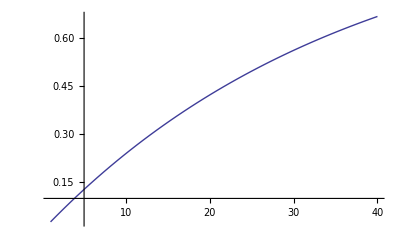

```mathematica
Plot[1-(36/37)^k,{k,1,40},PlotRange->All]
```

```mathematica
a=Sum[p[n]*n,{n,1,k}]
```

37-36^k 37^(1-k)-(36/37)^k k

```mathematica
Limit[a,{k->Infinity}]
```

{37}

```mathematica
h=Table[0,{i,0,10000}];nn=50000;r=RandomInteger[36,2*nn];kk=1;
For[i=0,i<nn,i++,
n=1;
If[kk>nn,kk=1;r=RandomInteger[36,2*nn]];
While[r[[kk++]]<36,n++];
h[[n]]+=1/nn;
]
```

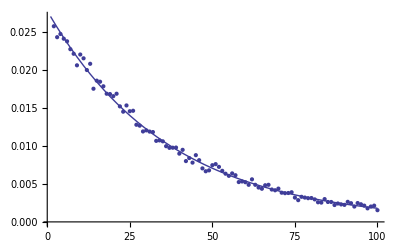

```mathematica
Show[Plot[p[n],{n,1,100}],ListPlot[h[[1;;100]]]]
```

```mathematica
RandomInteger[36]
```

33